## Camera resolution tests

## setup

```mathematica
imagedir=FileNameJoin[{NotebookDirectory[],"resolution_tests\\"}];
AppendTo[$Path, imagedir];
USAFlpmm[group_,element_]:=2^(group+(element-1)/6)//N; (*gives line pairs per mm on a USAF standard, where line pair is defined to be a bright and dark line*)
```

## Urban camera

As of 2021.03, the Urban camera CCD has been replaced with a PointGrey CCD. These are the resolution tests performed with a USAF 1951 1x standard for various wavelengths.

```mathematica
{{"Wavelength", "Pixels/μm", "Date"}, {650, 12.37, 2021/3/15}, {780, 12.12, 2021/3/15}, {852, 12.02, 2021/3/15}}
```

### 650

```mathematica
img = ColorConvert[Import["urban_camera_650_fault_finder_G7_USAF_1951_1x_20210315.png"],"grayscale"];
Show[img,ImageSize->Medium]
```

-Graphics-

```mathematica
data = ImageData[img];
data = data-data[[10,10]];(*subtract off the background, assuming a pixel away from the interesting stuff is representative*)
data = Replace[data,_?Negative-> 0,{2}];
data = data/Max[data]; 
lenx = data//Length
leny= data[[1]]//Length
```

960

1280

```mathematica
Show[Image[data],ImageSize->Medium]
```

-Graphics-

```mathematica
Image[data[[280;;380,60;;220]]](*7,6 using this*)
```

-Graphics-

```mathematica
Image[data[[290;;410,280;;480]]](*7,5*)
```

-Graphics-

```mathematica
group=7;
elem=6;
```

```mathematica
rowAvg=Sum[data[[i,60;;220]],{i,280,380}];
rowAvg/=Max[rowAvg];
```

{μ→32.3185,a→27.1156,σ→4.96391}

pixels per μm in object plane= 12.37

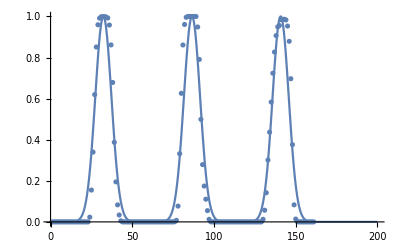

```mathematica
(*model = Piecewise[{{b,x<x0},{1,x0<=x<x0+a},{b,x0+a<=x<x0+2a},{1,x0+2a<=x<x0+3a},{b,x0+3a<=x<x0+4a},{1,x0+4a<=x<x0+5a},{b,x0+5a<=x<x0+6a},{None,x>6a}}];*)
(*fit =FindFit[rowAvg,model,{{x0,25},{a,25},{b,0.2}},x];*)
model = Exp[(-(x-μ)^2)/(2 σ^2)]+Exp[(-(x-(μ+2a))^2)/(2 σ^2)]+Exp[(-(x-(μ+4a))^2)/(2 σ^2)];
fit = FindFit[rowAvg,model,{{μ,30},{a,30},σ},x]
pixelsPerμm =2*Values[fit[[2]]]*USAFlpmm[group,elem]/1000; 
StringForm["pixels per μm in object plane= ``",NumberForm[pixelsPerμm,4]]
Show[ListPlot[rowAvg],Plot[model/.fit,{x,0,200}],PlotRange-> All]
```

### 780

```mathematica
img = ColorConvert[Import["urban_camera_780_G7_USAF_1951_1x_20210315.png"],"grayscale"];
Show[img,ImageSize->Medium]
```

-Graphics-

```mathematica
data = ImageData[img];
data = data-data[[10,10]];(*subtract off the background, assuming a pixel away from the interesting stuff is representative*)
data = Replace[data,_?Negative-> 0,{2}];
data = data/Max[data]; 
lenx = data//Length
leny= data[[1]]//Length
```

960

1280

```mathematica
Show[Image[data],ImageSize->Medium]
```

-Graphics-

```mathematica
Image[data[[290;;400,100;;280]]](*7,6*)
```

-Graphics-

```mathematica
Image[data[[280;;390,280;;480]]](*7,5 using this because more uniform than 7,6*)
```

-Graphics-

```mathematica
group=7;
elem=5;
```

```mathematica
rowAvg=Sum[data[[i,280;;480]],{i,280,390}];
rowAvg/=Max[rowAvg];
```

{μ→35.6998,a→29.837,σ→14.6021}

pixels per μm in object plane= 12.12

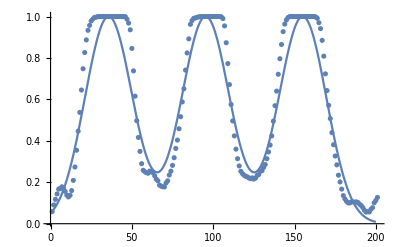

```mathematica
(*model = Piecewise[{{b,x<x0},{1,x0<=x<x0+a},{b,x0+a<=x<x0+2a},{1,x0+2a<=x<x0+3a},{b,x0+3a<=x<x0+4a},{1,x0+4a<=x<x0+5a},{b,x0+5a<=x<x0+6a},{None,x>6a}}];*)
(*fit =FindFit[rowAvg,model,{{x0,25},{a,25},{b,0.2}},x];*)
model = Exp[(-(x-μ)^2)/(2 σ^2)]+Exp[(-(x-(μ+2a))^2)/(2 σ^2)]+Exp[(-(x-(μ+4a))^2)/(2 σ^2)];
fit = FindFit[rowAvg,model,{{μ,40},{a,35},{σ,10}},x]
pixelsPerμm =2*Values[fit[[2]]]*USAFlpmm[group,elem]/1000; 
StringForm["pixels per μm in object plane= ``",NumberForm[pixelsPerμm,4]]
Show[ListPlot[rowAvg],Plot[model/.fit,{x,0,200}],PlotRange-> All]
```

### 852

```mathematica
img = ColorConvert[Import["urban_camera_852_G7_USAF_1951_1x_20210315.png"],"grayscale"];
Show[img,ImageSize->Medium]
```

-Graphics-

```mathematica
data = ImageData[img];
data = data-data[[10,10]];(*subtract off the background, assuming a pixel away from the interesting stuff is representative*)
data = Replace[data,_?Negative-> 0,{2}];
data = data/Max[data]; 
lenx = data//Length
leny= data[[1]]//Length
```

960

1280

```mathematica
Show[Image[data],ImageSize->Medium]
```

-Graphics-

```mathematica
leny
```

1280

```mathematica
Image[data[[290;;400,100;;280]]](*7,6*)
```

-Graphics-

```mathematica
Image[data[[290;;410,280;;480]]](*6,6. using this rather than 7,6 because more uniform line-to-line*)
```

-Graphics-

```mathematica
group=7;
elem=5;
```

```mathematica
rowAvg=Sum[data[[i,280;;480]],{i,290,410}];
rowAvg/=Max[rowAvg];
```

{μ→42.1142,a→29.5782,σ→10.1447}

pixels per μm in object plane= 12.02

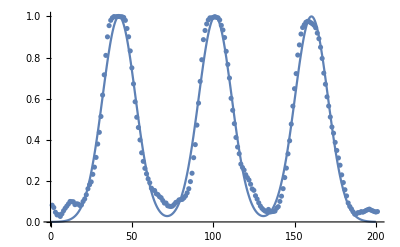

```mathematica
(*model = Piecewise[{{b,x<x0},{1,x0<=x<x0+a},{b,x0+a<=x<x0+2a},{1,x0+2a<=x<x0+3a},{b,x0+3a<=x<x0+4a},{1,x0+4a<=x<x0+5a},{b,x0+5a<=x<x0+6a},{None,x>6a}}];*)
(*fit =FindFit[rowAvg,model,{{x0,25},{a,25},{b,0.2}},x];*)
model = Exp[(-(x-μ)^2)/(2 σ^2)]+Exp[(-(x-(μ+2a))^2)/(2 σ^2)]+Exp[(-(x-(μ+4a))^2)/(2 σ^2)];
fit = FindFit[rowAvg,model,{{μ,40},{a,35},{σ,10}},x]
pixelsPerμm =2*Values[fit[[2]]]*USAFlpmm[group,elem]/1000; 
StringForm["pixels per μm in object plane= ``",NumberForm[pixelsPerμm,4]]
Show[ListPlot[rowAvg],Plot[model/.fit,{x,0,200}],PlotRange-> All]
```